```mathematica
Inclusion of drive frequency in steady state
```

drive frequency in Inclusion of state steady

```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
(** cgs units **) 
(** constants **)
c=29979245800;
(*ℏ=1.0546*10^-27;*)
ℏ=6.582119569*10^-16; (* [eV*s] *)
e=4.8032*10^-10;
```

```mathematica
(** Parameters [rad/s] **)
we=1.4321*10^15;
γe=0.0412*10^13+9.4498*10^13;
wc[U_,Nc_]:=(we-20*10^-3/ℏ)+U*Nc
γc=0+2.6435*10^9;
g=5.0440*10^11;
wc[U,1]
Δc[ω_,U_,Nc_]:= ω-(wc[U,Nc]-ⅈ*γc/2)
Δe[ω_]:= ω-(we-ⅈ*γe/2)
Edrive[na_]:=Sqrt[na] * Abs[(ⅈ*γc/2*Δe[wc[U,0]] - g^2)]/g
```

1.40171×10^15+U

```mathematica
(**Fano Param**)
ζe[ω_]:=g^2/((ω-we)^2+(γe/2)^2)
ζc[ω_,U_,Nc_]:=g^2/((ω-wc[U,Nc])^2+(γc/2)^2)
Ω[ω_,U_,Nc_]:= wc[U,Nc] + ζe[ω](ω-we)
Γc[ω_]:=γc+(ζe[ω]*γe)
Γe[ω_,U_,Nc_]:=γe+(ζc[ω,U,Nc]*γc)
ϵ[ω_,U_,Nc_]:=(ω-Ω[ω,U,Nc])/(Γc[ω]/2)
q[ω_,U_,Nc_]:=-(wc[U,Nc]-ⅈ*γc/2-Ω[ω,U,Nc])/(Γc[ω]/2)
```

## Spectrum

```mathematica
βss[ω_,U_,Nc_]:=Γe[ω,U,Nc]/γe*Abs[(q[ω,U,Nc]+ϵ[ω,U,Nc])/(ϵ[ω,U,Nc]+ⅈ)]^2
αss[ω_,U_,Nc_,na_]:=g^2(Edrive[na])^2/Abs[(Δc[ω,U,Nc]*Δe[ω]-g^2)]^2
```

```mathematica
Spec1 = {αss[(det*10^-3/ℏ+we),U,0,1],αss[(det*10^-3/ℏ+we),Γc[wc[U,0]],1,1]};
Spec2 ={βss[(det*10^-3/ℏ+we),U,0], βss[(det*10^-3/ℏ+we),Γc[wc[U,0]],1]};
Spec3 = {αss[(det*10^-3/ℏ+we),U,0,1],βss[(det*10^-3/ℏ+we),U,0],
αss[(det*10^-3/ℏ+we),Γc[wc[U,0]],1,1],βss[(det*10^-3/ℏ+we),Γc[wc[U,0]],1]};
```

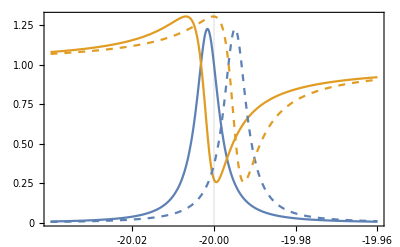

```mathematica
Plot[Spec3,{det,-20.04,-19.96},
GridLines->{{{-20,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"S(\\omega_L)",None},
{"\\hbar(\\omega_L - \\omega_e) \\:\\mathrm{meV}",None}},
PlotLegends->MaTeX@
{"<a^{\\dagger}a>","\\frac{<b^{\\dagger}b>_g}{<b^{\\dagger}b>_{g=0}}"},
PlotLabel->MaTeX@
"\\omega_{L}=\\omega_c",
FrameTicks->All,
FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
PlotRange->All,
PlotStyle->{{ColorData[97,1]},{ColorData[97,2]},
{Dashed,ColorData[97,1]},{Dashed,ColorData[97,2]}}, (*for Spec3 plot*)
(*PlotStyle->{{ColorData[97,2]},
{Dashed,ColorData[97,2]} },*)
 Exclusions->None]
```

## Second order correlation

```mathematica
g2n[ω_,U_,Nc_,na_]:=(1/na)*αss[ω,U,Nc,(na-1)] (* Fock state *)
g2α[ω_,U_,Nc_]:=αss[ω,U,Nc,1] (* Coherenet state *)
```

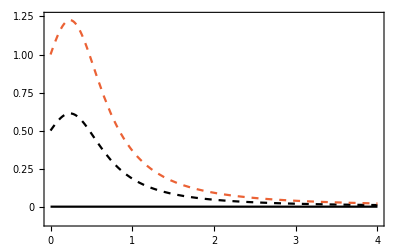

```mathematica
(*plot*)
g2plt1 = g2n[wc[U,0],x*Γc[wc[U,0]],1,1];
g2plt2 = g2n[wc[U,0],x*Γc[wc[U,0]],1,2];
g2plt3 = g2α[wc[U,0],x*Γc[wc[U,0]],1];
g2plt = {g2plt1,g2plt2,g2plt3};

Plot[g2plt,{x,0,4},

Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{
{"g^{(2)}_{ss}(\\omega_L=\\omega_c; N_c=1)",None},
{" U / \\Gamma ",None} },
PlotLegends->MaTeX@
{"|n_{c} = 1 \\rangle",
"|n_{c} = 2 \\rangle",
"|\\alpha \\rangle" },
(*PlotLabel->MaTeX@
"\\omega_{L}=\\omega_c",*)
FrameTicks->All,
FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
PlotRange->{{0,4},{-0.1,1.25}},
PlotStyle->{ {Solid,Black},{Dashed,Black},
{Dashed,ColorData[97,4]} } ,
 Exclusions->None]
```

### Probability of finding n photons in the coherent state (Poison distribution)

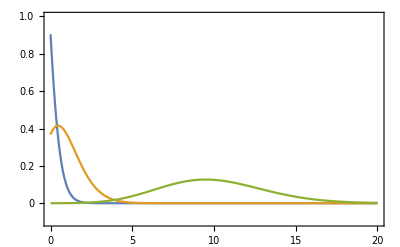

```mathematica
p[n_,N_]:=N^n*Exp[-N]/n!;
Plot[{ p[n,0.1],p[n,1],p[n,10] },{n,0,20},

Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{
{" P(n) ",None},
{" n ",None} },
PlotLegends->MaTeX@
{" \\vert \\alpha \\vert^2 = 0.1 ",
" \\vert \\alpha \\vert^2 = 1 ",
" \\vert \\alpha \\vert^2 = 10 "  },
(*PlotLabel->MaTeX@
"\\omega_{L}=\\omega_c",*)
FrameTicks->All,
FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
PlotRange->{{0,20},{-0.1,1}},
(*PlotStyle->{ {Solid,Black},{Dashed,Black},
{Dashed,ColorData[97,4]} } ,*)
 Exclusions->None]
```

## Estimates

### Relation between Fano resonance shift and chi3 (n2), with regards to the local intensity (I)

```mathematica
λ=1566*10^-7; (* [cm] *)
k=2*π/λ
n0=1.444 (* [1] *)
n2=1.15*10^-12(* [cm^2/W] *)
Γ=6.25*10^-6/ℏ (* [rad/s] *)
Intensity1=Γ/(c*k*n2)
Intensity2=Γc[wc[U,0]]/(c*k*n2)
```

(10000000 π)/783

1.444

1.15×10^-12

9.49542×10^9

6.86448×10^6

7.40871×10^6

```mathematica
Γc[wc[U,0]]* ℏ
```

6.74552×10^-6

```mathematica
6.25*10^-6/ℏ
```

9.49542×10^9

```mathematica
γe*ℏ
γc*ℏ
```

6.58212×10^-16 γp

1.73998×10^-6